```mathematica
Switch[$MachineName,"twistor",SetDirectory["F:\\aitor ingelmo\\comsol"],"joseluis-pc",SetDirectory["C:\\Users\\joseluis\\OneDrive - Universidad de Alcala\\\\biblioteca_dropbox_propios\\reviews\\complex integration"],"delldjcdd63",SetDirectory["C:\\Users\\dyson\\OneDrive - Universidad de Alcala\\\\biblioteca_dropbox_propios\\reviews\\complex integration"]]
```

F:\aitor ingelmo\comsol

```mathematica
fileEx=OpenRead["microstrip_patch_antenna_Ex.txt"]
```

InputStream[microstrip_patch_antenna_Ex.txt,66]

```mathematica
fileEy=OpenRead["microstrip_patch_antenna_Ey.txt"]
```

InputStream[microstrip_patch_antenna_Ey.txt,67]

```mathematica
fileEz=OpenRead["microstrip_patch_antenna_Ez.txt"]
```

InputStream[microstrip_patch_antenna_Ez.txt,68]

```mathematica
Do[Read[fileEx,String],{8}]
```

```mathematica
Do[Read[fileEy,String],{8}]
```

```mathematica
Do[Read[fileEz,String],{8}]
```

```mathematica
headerdataEx=Read[fileEx,String]
```

% x                       y                        z                        emw.Ex (V/m) @ freq=1.5750E9

```mathematica
headerdataEy=Read[fileEy,String]
```

% x                       y                        z                        emw.Ey (V/m) @ freq=1.5750E9

```mathematica
headerdataEz=Read[fileEz,String]
```

% x                       y                        z                        emw.Ez (V/m) @ freq=1.5750E9

```mathematica
dataEx=ReadList[fileEx,String];
```

```mathematica
dataEy=ReadList[fileEy,String];
```

```mathematica
dataEz=ReadList[fileEz,String];
```

```mathematica
Close[fileEx]
```

microstrip_patch_antenna_Ex.txt

```mathematica
Close[fileEy]
```

microstrip_patch_antenna_Ey.txt

```mathematica
Close[fileEz]
```

microstrip_patch_antenna_Ez.txt

```mathematica
datasetExSplitted=StringSplit[dataEx];
```

```mathematica
datasetEySplitted=StringSplit[dataEy];
```

```mathematica
datasetEzSplitted=StringSplit[dataEz];
```

```mathematica
Dimensions[datasetExSplitted]
```

{1000000,4}

```mathematica
datavaluesEz=ToExpression[Map[Thread,Thread[f[datasetExSplitted,a]]]/.{a->{"E"->"*10^","i"->"I","NaN"->"0"},f->StringReplace}];
```

```mathematica
Dimensions[datavaluesEz]
```

{1000000,4}

```mathematica
dimension=100
```

100

```mathematica
xcoordinates=Union[Part[datavaluesEz,All,1]];
```

```mathematica
ycoordinates=Union[Part[datavaluesEz,All,2]];
```

```mathematica
zcoordinates=Union[Part[datavaluesEz,All,3]];
```

```mathematica
xcoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[1]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
ycoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[2]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
zcoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[3]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
datavaluesEzTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[4]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
Dimensions[xcoordinatesTensor]
```

{100,100,100}

```mathematica
Dimensions[datavaluesEzTensor]
```

{100,100,100}

```mathematica
index1=58
```

58

```mathematica
zcoordinateselected1=zcoordinates[[index1]] 1.*^-3
```

0.015

```mathematica
xcoordinatesPlane1=Part[xcoordinatesTensor,All,All,index1];
```

```mathematica
ycoordinatesPlane1=Part[ycoordinatesTensor,All,All,index1];
```

```mathematica
zcoordinatesPlane1=Part[zcoordinatesTensor,All,All,index1];
```

```mathematica
datavaluesEzPlane1=Part[datavaluesEzTensor,All,All,index1];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"DarkBands",
PlotLegends->BarLegend[{"DarkBands",{0,20}}],FrameTicks->Automatic]
```

-Graphics-

```mathematica
datavaluesEzPlane1w=Fourier[datavaluesEzPlane1,FourierParameters->{-1,1}];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1w],PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
ListPlot3D[Abs[datavaluesEzPlane1w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[10 Log[10.,Abs[datavaluesEzPlane1w]],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
deltax=(xcoordinates[[2]]-xcoordinates[[1]]) 1*^-3
```

0.002

```mathematica
deltay=(ycoordinates[[2]]-ycoordinates[[1]]) 1*^-3
```

0.002

```mathematica
Lx=(xcoordinates[[-1]]-xcoordinates[[1]]) 1*^-3
```

0.198

```mathematica
Ly=(ycoordinates[[-1]]-ycoordinates[[1]]) 1*^-3
```

0.198

```mathematica
Nx=Length[xcoordinates]
```

100

```mathematica
Ny=Length[ycoordinates]
```

100

```mathematica
deltakx=2 Pi/(deltax Nx)
```

31.4159

```mathematica
deltaky=2 Pi/(deltay Ny)
```

31.4159

```mathematica
freq=1.575*^9
```

1.575×10^9

```mathematica
c0=299792458
```

299792458

```mathematica
k0=2 Pi freq/c0
```

33.0096

```mathematica
lambda0=c0/freq
```

0.190344

```mathematica
kxcoordinatesMatrix=deltakx Table[If[i≤dimension/2,i-1,i-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
a=Table[If[i≤dimension/2,i-1,i-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
Dimensions[kxcoordinatesMatrix]
```

{100,100}

```mathematica
ListDensityPlot[kxcoordinatesMatrix,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
kycoordinatesMatrix=deltaky Table[If[j≤dimension/2,j-1,j-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
ListDensityPlot[kycoordinatesMatrix,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
k0
```

33.0096

```mathematica
w2=k0^2-kxcoordinatesMatrix^2-kycoordinatesMatrix^2;
```

```mathematica
ListDensityPlot[w2,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
w=Conjugate[Sqrt[w2]];
```

```mathematica
ListDensityPlot[Re[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Im[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot3D[Re[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[10 Log[10.,Re[w]+1*^-12],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
index2=66
```

66

```mathematica
zcoordinateselected2=zcoordinates[[index2]]*1.*^-3
```

0.031

```mathematica
phaseShift=Exp[-I w (zcoordinateselected2-zcoordinateselected1)];
```

```mathematica
datavaluesEzPlane2w=datavaluesEzPlane1w*phaseShift;
```

```mathematica
datavaluesEzReconstructedPlane2=InverseFourier[datavaluesEzPlane2w,FourierParameters->{-1,1}];
```

```mathematica
datavaluesEzReconstructedPlane2[[1]][[1]]
```

0.0047515-0.00636668 ⅈ

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzReconstructedPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
datavaluesEzPlane2=Part[datavaluesEzTensor,All,All,index2];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

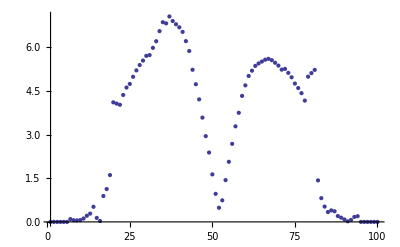

```mathematica
ListPlot[Abs[Part[datavaluesEzPlane2,30,All]],PlotRange->All]
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2-datavaluesEzReconstructedPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
indicesOutsideModelledArea=Position[datavaluesEzPlane2,0];
```

```mathematica
Dimensions[indicesOutsideModelledArea]
```

{2690,2}

```mathematica
Length[indicesOutsideModelledArea]
```

2690

```mathematica
datavaluesEzReconstructedPlane2Reduced=Table[If[datavaluesEzPlane2[[i]][[j]]==0,0,datavaluesEzReconstructedPlane2[[i]][[j]]],{i,1,dimension},{j,1,dimension}];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzReconstructedPlane2Reduced],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2-datavaluesEzReconstructedPlane2Reduced],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-